area of overlap as function of distance from optimum (d) and angle between optima (θ)

```mathematica
A[d_,θ_]:=2 d^2 ArcCos[x/(2d)]-x/2  √(4 d^2-x^2)/.x->d √(2(1-Cos[θ]))
```

overlap declines with angle (here from 0 to 180 degrees) for any distance

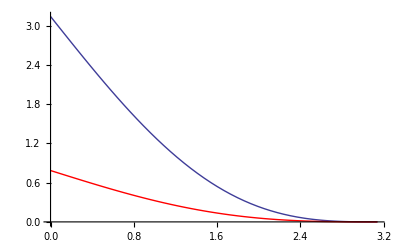

```mathematica
Show[
Plot[A[d,θ]/.d->1,{θ,0,π}],
Plot[A[d,θ]/.d->0.5,{θ,0,π},PlotStyle->Red],
PlotRange->All
]
```

overlap increases with distance for any angle

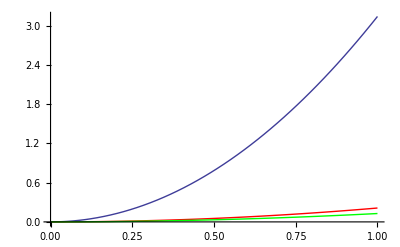

```mathematica
Show[
Plot[A[d,θ]/.θ->0,{d,0,1}],
Plot[A[d,θ]/.θ->90,{d,0,1},PlotStyle->Red],
Plot[A[d,θ]/.θ->180,{d,0,1},PlotStyle->Green],
PlotRange->All
]
```

fraction overlap

note that the fraction overlap is independent of the distance, d:

```mathematica
fA=Simplify[A[d,θ]/A[d,0],d>0]
```

(2 ArcCos[√(Sin[θ/2]^2)]-√(Sin[θ]^2))/π

and declines from 1 to 0 with angle

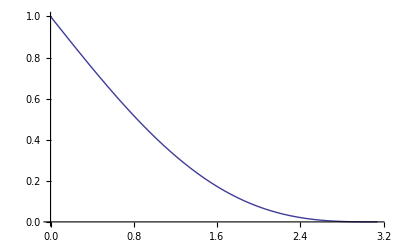

```mathematica
Show[
Plot[A[d,θ]/A[d,0]/.d->1,{θ,0,π}],
PlotRange->All
]
```

the fraction overlap is 0 when the angle is 180 degrees

```mathematica
A[d,θ]/A[d,0]/.θ->π
```

0

there is perfect overlap when the angle is 0

```mathematica
A[d,θ]/A[d,0]/.θ->0
```

1

when the angle is 90 degrees the fraction overlap is

```mathematica
Simplify[A[d,θ]/A[d,0]/.θ->π/2,d>0]
```

1/2-1/π

```mathematica
(2 ArcCos[√(Sin[θ/2]^2)]-√(Sin[θ]^2))/π
```

(2 ArcCos[√(Sin[θ/2]^2)]-√(Sin[θ]^2))/π

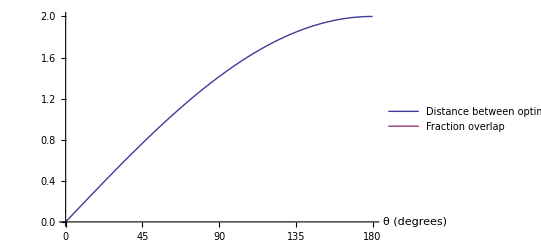

```mathematica
Plot[
{
d*√(2(1-Cos[θ*π/180]))/.d->1,
A[d,θ*π/180]/A[d,0]/.d->1
},
{θ,0,180},
Ticks->{{0,45,90,135,180},Automatic},
AxesLabel->{"θ (degrees)"},
PlotLegends->{"Distance between optima","Fraction overlap"}
]
```

```mathematica
(d*√(2(1-Cos[θ])))/(d*√(2(1-Cos[π])))
```

(√(1-Cos[θ]))/(√2)

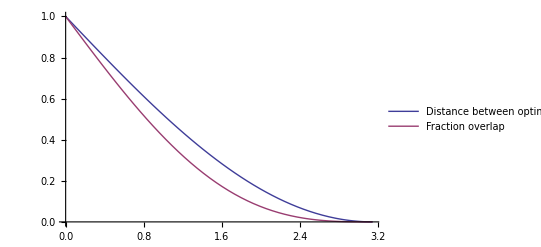

```mathematica
Plot[{1-(√(1-Cos[θ]))/(√2),(2 ArcCos[√(Sin[θ/2]^2)]-√(Sin[θ]^2))/π},{θ,0,π},PlotLegends->{"Distance between optima","Fraction overlap"}]
```

```mathematica
A[x_,d_]:=2 d^2 ArcCos[x/(2d)]-x/2  √(4 d^2-x^2)
```

```mathematica
A[x,r]/A[0,r]//Simplify
```

(-1/2 x √(4 r^2-x^2)+2 r^2 ArcCos[x/(2 r)])/(π r^2)

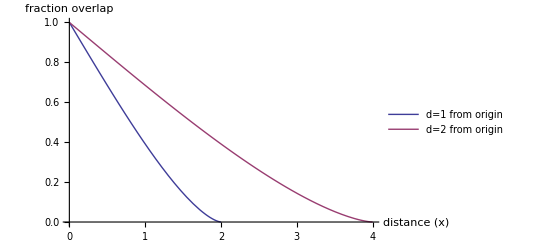

```mathematica
Plot[{A[x,d]/A[0,d]/.d->1,A[x,d]/A[0,d]/.d->2},{x,0,4},AxesLabel->{"distance (x)","fraction overlap"},
PlotLegends->{"d=1 from origin","d=2 from origin"}]
```

## volume overlap m=3

http://mathworld.wolfram.com/Sphere-SphereIntersection.html

volume overlap bw spheres of radii r and R, with distance d between the centres

```mathematica
(π (R+r-d)^2(d^2+2d r-3 r^2+2d R+6r R-3 R^2))/(12d)
```

(π (-d+r+R)^2 (d^2+2 d r-3 r^2+2 d R+6 r R-3 R^2))/(12 d)

when both have same radii

```mathematica
%/.R->r//Simplify
```

1/12 π (d-2 r)^2 (d+4 r)

and when the distance between them is determined by the distance from the origin (also r) and the angle between them

```mathematica
V[r_,θ_]:=1/12 π (d-2 r)^2 (d+4 r)/.d->r √(2(1-Cos[θ]))
```

then the fraction overlap is

```mathematica
fV=V[r,θ]/V[r,0]//Simplify
```

1/16 (-2+√(2-2 Cos[θ]))^2 (4+√(2-2 Cos[θ]))

which is independent of the distance to the optimum, r.

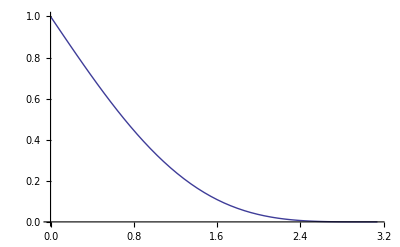

```mathematica
Plot[fV,{θ,0,π}]
```

Comparing to the 2 dimensional case

```mathematica
fA/.θ->θ*180/π
```

(2 ArcCos[√(Sin[(90 θ)/π]^2)]-√(Sin[(180 θ)/π]^2))/π

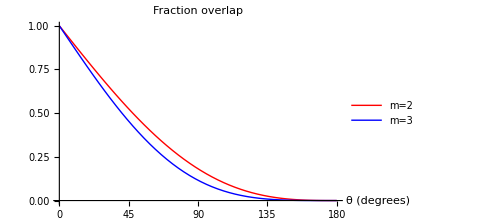

```mathematica
Plot[{fA/.θ->deg*π/180,fV/.θ->deg*π/180},{deg,0,180},PlotStyle->{{Red},{Blue}},
Ticks->{{0,45,90,135,180},Automatic},
AxesLabel->{"θ (degrees)"},
PlotLegends->{"m=2","m=3"},
PlotLabel->"Fraction overlap"
]
```

we see that the volume overlap (m=3) decreases even faster than the area overlap